Quantum Amplitude Amplification |

Quantum Amplitude Amplification (QAA)paclet:QuantumMob/Q3/tutorial/QuantumAmplitudeAmplification#1404287834 | Oblivious Amplitude Amplification (OAA)paclet:QuantumMob/Q3/tutorial/QuantumAmplitudeAmplification#635509592

Quantum amplitude amplification is a quantum algorithmic technique used to increase the probability of finding a desired outcome in a quantum system. It generalizes the concept of Grover's algorithm, which is specifically designed for unstructured search problems. In quantum amplitude amplification, the basic idea is to start with a superposition of quantum states, each with a certain amplitude, and iteratively apply a sequence of quantum operations to amplify the amplitudes of the states corresponding to desired outcomes while reducing the amplitudes of the undesired ones. This is achieved through a process involving quantum reflection and interference, which systematically increases the likelihood of measuring the correct state upon observation. The technique is widely applicable in quantum algorithms, providing a quadratic speedup over classical counterparts for a variety of search and optimization problems.

Quantum Amplitude Amplification (QAA)

Consider a unitary operator U such that

ψ':=Uψ=ϕ √p+ϕ^⊥√(1-p),

where ϕ is the “good” (or desired) state and ϕ^⊥ is the “bad” state, ϕϕ^⊥=0, and p is the probability to achieve the good state. The input state ψ is typically set to 0^(⊗n), but here we consider a more general case. Although we usually do not have a direct access to the good state itself, it is assumed that we do have an access to the oracle

-Z_ϕ:=I-2ϕϕ,

which “marks” the good state by the phase factor -1 or, equivalently, may be regarded as a reflection about the hyperplane perpendicular to ϕ.

Following the idea behind the quantum search algorithm, we combine the oracle Z_ϕ and the reflection about the state ψ',
	Z_ψ':=2ψ'ψ'-I=U(2ψψ-I)U^†=U Z_ψ U^†,

to get the rotation by angle 2θ (sinθ:=√p)

Ω_AA:=-U Z_ψ U^†Z_ϕ≡-Z_ψ' Z_ϕ

toward the desired state.

Technically, it is interesting to note that the amplitude amplification process Ω_AA preserves the two-dimensional subspace spanned by ϕ and Uψ as first observed by Brassard and Høyer (1997) and rediscovered by Grover (1998); see Figure 1 below.

-Graphics-

Figure 1. Geometric demonstration of the quantum amplitude amplification process Ω_AA:=-U Z_ψ U^†Z_ϕ≡-Z_ψ' Z_ϕ, where ψ':=Uψ. Note that to construct the unitary operation Ω_AA requires the knowledge of the initial state ψ, which is typically set to 0^(⊗n).

### Demonstration

Consider a quantum register of a finite number of qubits:

```mathematica
$n=2;
$N=Power[2,$n];
```

```mathematica
Let[Qubit,S]
SS=S[Range@$n,$]
```

{S_(,,1),S_(,,2)}

Consider an algorithm (or, equivalently, a unitary operator) in a numerical matrix form for convenience:

```mathematica
UU=Rotation[Pi/3,S[1,3]]**Rotation[Pi/4,S[2,1]];
UU=Matrix[UU,SS]//N;
UU//IntegerChop//MatrixForm
```

(0.800103-0.46194 ⅈ | -0.191342-0.331414 ⅈ | 0 | 0
-0.191342-0.331414 ⅈ | 0.800103-0.46194 ⅈ | 0 | 0
0 | 0 | 0.800103+0.46194 ⅈ | 0.191342-0.331414 ⅈ
0 | 0 | 0.191342-0.331414 ⅈ | 0.800103+0.46194 ⅈ)

Choose an initial state:

```mathematica
in=S[1,6]**S[2,6]**Ket[];
in=Matrix[in,SS];
in//Normal
```

{1/2,1/2,1/2,1/2}

Get the output state through the algorithm:

```mathematica
out=UU.in;
out//Normal
```

{0.304381-0.396677 ⅈ,0.304381-0.396677 ⅈ,0.495722+0.0652631 ⅈ,0.495722+0.0652631 ⅈ}

We want the output state to be close to a desired "good" state:

```mathematica
good=GHZState[SS]//First
good=Matrix[good];
good//Normal
```

(0_(,,S_(,,1))0_(,,S_(,,2))+1_(,,S_(,,1))1_(,,S_(,,2)))/(√2)

{1/(√2),0,0,1/(√2)}

Check the fidelity between the output from the algorithm and the desired state:

```mathematica
fdl=Fidelity[good,out]//N
```

0.612372

Before constructing the amplitude amplification (AA) operator, construct the "phase marker" operators:

```mathematica
Zin=2*Dyad[in,in]-One[$N];
Zgd=2*Dyad[good,good]-One[$N];
```

Construct the AA operator:

```mathematica
AA=UU.Zin.ConjugateTranspose[UU].Zgd;
AA//ArrayShort
```

(0.25-0.433013 ⅈ | -0.5 | -0.25+0.433013 ⅈ | -0.5
0.25-0.433013 ⅈ | 0.5 | -0.25+0.433013 ⅈ | 0.5
0.5 | -0.25-0.433013 ⅈ | 0.5 | 0.25+0.433013 ⅈ
-0.5 | -0.25-0.433013 ⅈ | -0.5 | 0.25+0.433013 ⅈ)

Apply the AA operator on the output state:

```mathematica
mid=AA.out
```

SparseArray[…]

The fidelity has been improved:

```mathematica
fdl=Fidelity[good,mid]//N
```

0.918559

If you apply the AA operator too many times, then the fidelity gets worse again:

```mathematica
mid=MatrixPower[N@AA,2].out;
fdl=Fidelity[good,mid]//N
```

0.153093

Repeating the AA operation, the fidelity oscillates:

```mathematica
mid=MatrixPower[N@AA,5].out;
fdl=Fidelity[good,mid]//N
```

0.822875

Oblivious Amplitude Amplification (OAA)

Oblivious amplitude amplification (OAA) is a generalization of the quantum amplitude amplification algorithm. Unlike the standard amplitude amplification, OAA does not require knowledge of the initial state or a full reflection about it. Instead, it amplifies the amplitude of a target state while handling scenarios where the initial state is unknown or “oblivious.”

Let U be a unitary operator on the quantum register of n qubits. Introduce an ancillary quantum register of m qubits, and let V be a unitary gate on the overall quantum register such that

V(0^m⊗ψ)=0^m⊗(Uψ)√p+Φ^⊥√(1-p),

where Φ^⊥ is a normalized state that is not of our interest, such that ΠΦ^⊥=0, where

Π:=(0^m0^m)⊗I_n 
and I_k denotes the identity matrix on k qubits, i.e., the 2^k×2^k (not k×k) identity matrix.

In the matrix form, the 2^(m+n)×2^(m+n) unitary matrix V is a block encoding of the 2^n×2^n unitary matrix U,

V=(√p U | *
* | *) .

Here, it is important that U is unitary. The goal is to increase the success probability for 0^m on the ancillary register.

For later use, we define the product states

Ψ:=0^m⊗ψ  ,       Φ:=0^m⊗(Uψ)

so that the operation of V reads as

VΨ=Φ √p+Φ^⊥√(1-p).

If you follow the standard amplitude amplification idea in the above, you need an oracle

(I_m⊗U)(I_(m+n)-20^m0^m⊗ψψ)(I_m⊗U^†)

and the reflection in VΨ,
	V(20^m0^m⊗ψψ-I_(m+n))V^†.

Note that both require an access to the initial state ψ or the reflection about it.

However, the OAA lemma (Berry et al., 2014https://doi.org/10.1145/2591796.2591854) asserts that the goal can be achieved by just repeatedly applying

Ω_OAA:=-V Z_Π V^†Z_Π    with    Z_Π:=(20^m0^m-I_m)⊗I_n.

Here, the crucial point is that it does not require a copy (or knowledge) of the initial state ψ at all.

To understand the OAA lemma, the key observation is that over the transform V (and hence the OAA process), the state remains in the two-dimensional subspace spanned by Φ and VΨ (Berry et al., 2014) as shown in Figure 2. This can be clearly seen by recalling the unitary gate V

VΨ=Φ √p+Φ^⊥√(1-p),

and defining a new state Ψ^⊥ through

VΨ^⊥=Φ √(1-p)-Φ^⊥√p.

One can see that not only ΨΨ^⊥=0 but also ΠΨ^⊥=0; hence, Z_Π Ψ_⊥=-Ψ_⊥. Then, one can show that
	Ω_OAA^k VΨ=VΨcos(2kθ)+VΨ_⊥sin(2kθ)=Φsin((2k+1)θ)+Φ_⊥cos((2k+1)θ)
with sin(θ):=√p.

-Graphics-

Figure 2. Geometric demonstration of the oblivious amplitude amplification process Ω_OAA:=-VZ V^†Z. Unlike the standard amplitude amplification, Ω_OAA does not require the information about initial state.

### Demonstration

Set the number of qubits in the ancillary and system register respectively:

```mathematica
$m=2;
$n=2;
```

Set the ancillary and system registers:

```mathematica
Let[Qubit,A,S]
AA=A[Range@$m,$]
SS=S[Range@$n,$]
AS=Join[AA,SS];
```

{A_(,,1),A_(,,2)}

{S_(,,1),S_(,,2)}

Take a unitary operator on the system register:

```mathematica
UU=Rotation[Pi/3,S[1,3]]**Rotation[Pi/4,S[2,2]]
UU=Matrix[UU,SS]//N;
UU//IntegerChop//MatrixForm
```

Exp(-1/6 ⅈ π S_(,,1)^(,,Z))Exp(-1/8 ⅈ π S_(,,2)^(,,Y))

(0.800103-0.46194 ⅈ | -0.331414+0.191342 ⅈ | 0 | 0
0.331414-0.191342 ⅈ | 0.800103-0.46194 ⅈ | 0 | 0
0 | 0 | 0.800103+0.46194 ⅈ | -0.331414-0.191342 ⅈ
0 | 0 | 0.331414+0.191342 ⅈ | 0.800103+0.46194 ⅈ)

Embed the unitary operator into the larger register including the ancillary and system registers:

```mathematica
$p=0.1;
```

```mathematica
VV=BlockEncoding[Sqrt[$p]*UU,SS,AA]
VV=Matrix[VV,Join[AA,SS]];
VV//ArrayShort
```

BlockEncoding[…]

(0.253015-0.146078 ⅈ | -0.104802+0.0605076 ⅈ | 0 | 0 | …
0.104802-0.0605076 ⅈ | 0.253015-0.146078 ⅈ | 0 | 0 | …
0 | 0 | 0.253015+0.146078 ⅈ | -0.104802-0.0605076 ⅈ | …
0 | 0 | 0.104802+0.0605076 ⅈ | 0.253015+0.146078 ⅈ | …
… | … | … | … | …)

Construct the "phase marker" operator:

```mathematica
ZZ=(2Ket[AA]**Bra[AA]-1)
ZZ=Matrix[ZZ,AS];
```

-1+2 0_(,,A_(,,1))0_(,,A_(,,2))0_(,,A_(,,1))0_(,,A_(,,2))

Construct the oblivious amplitude amplification (OAA) operator:

```mathematica
OAA=-VV.ZZ.ConjugateTranspose[VV].ZZ;
OAA//IntegerChop//MatrixForm
```

(0.8 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.8 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.8 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.8 | 0 | 0 | 0 | 0.6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.6 | 0 | 0 | 0 | 0.8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.6 | 0 | 0 | 0 | 0.8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.6 | 0 | 0 | 0 | 0.8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.6 | 0 | 0 | 0 | 0.8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

Take an arbitrary input state of the form 0^m⊗ψ:

```mathematica
in=Ket[AA->0]**First[GHZState[SS]]
in=Matrix[in];
in//Normal
```

(0_(,,A_(,,1))0_(,,A_(,,2))0_(,,S_(,,1))0_(,,S_(,,2)))/(√2)+(0_(,,A_(,,1))0_(,,A_(,,2))1_(,,S_(,,1))1_(,,S_(,,2)))/(√2)

{1/(√2),0,0,1/(√2),0,0,0,0,0,0,0,0,0,0,0,0}

Apply the embedded unitary operator on the input state to get the output state:

```mathematica
out=VV.in//Chop;
ExpressionFor[out,AS]
```

(0.178909-0.103293 ⅈ) 0_(,,A_(,,1))0_(,,A_(,,2))0_(,,S_(,,1))0_(,,S_(,,2))+(0.0741063-0.0427853 ⅈ) 0_(,,A_(,,1))0_(,,A_(,,2))0_(,,S_(,,1))1_(,,S_(,,2))-(0.0741063+0.0427853 ⅈ) 0_(,,A_(,,1))0_(,,A_(,,2))1_(,,S_(,,1))0_(,,S_(,,2))+(0.178909+0.103293 ⅈ) 0_(,,A_(,,1))0_(,,A_(,,2))1_(,,S_(,,1))1_(,,S_(,,2))+(0.536726-0.309879 ⅈ) 0_(,,A_(,,1))1_(,,A_(,,2))0_(,,S_(,,1))0_(,,S_(,,2))+(0.222319-0.128356 ⅈ) 0_(,,A_(,,1))1_(,,A_(,,2))0_(,,S_(,,1))1_(,,S_(,,2))-(0.222319+0.128356 ⅈ) 0_(,,A_(,,1))1_(,,A_(,,2))1_(,,S_(,,1))0_(,,S_(,,2))+(0.536726+0.309879 ⅈ) 0_(,,A_(,,1))1_(,,A_(,,2))1_(,,S_(,,1))1_(,,S_(,,2))

We want the output state to be close to the desired "good" state:

```mathematica
good=MatrixEmbed[UU,SS,AS].in
```

SparseArray[…]

Check the fidelity between the desired and output states:

```mathematica
fdl=Fidelity[good,out]
```

0.316228

Apply the OAA operator to improve the fidelity:

```mathematica
mid=OAA.out
fdl=Fidelity[good,mid]
```

SparseArray[…]

0.822192

Repeating the OAA operations, the fidelity oscillates:

```mathematica
mid=NestList[OAA.#&,out,12];
fdl=Map[Fidelity[good,#]&,mid]
```

{0.316228,0.822192,0.99928,0.776655,0.243369,0.387265,0.862993,0.993524,0.726645,0.169108,0.456072,0.898823,0.982045}

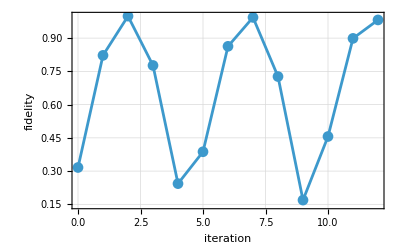

```mathematica
ListLinePlot[fdl,
DataRange->{0,12},
PlotMarkers->Automatic,
FrameLabel->{"iteration","fidelity"}]
```

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Search Algorithm
▪Block Encoding
▪Quantum Computation: Overview
▪Quantum Information Systems with Q3

| Related Links
▪G . Brassard and P. Høyer (1997)https://doi.org/10.1109%2FISTCS.1997.595153, Proceedings of the Fifth Israeli Symposium on Theory of Computing and Systems, “An exact quantum polynomial-time algorithm for Simon’s problem.” 
▪Lov K . Grover (1998)https://doi.org/10.1103/PhysRevLett.80.4329, Physical Review Letters 80, 4329 (1998), “Quantum Computers Can Search Rapidly by Using Almost Any Transformation.”
▪D. W. Berry et al. (2014)https://doi.org/10.1145/2591796.2591854, Proceedings of the 2014 ACM symposium on Theory of Computing (STOC 2014), “Exponential improvement in precision ∗ for simulating sparse Hamiltonians.”
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).